```mathematica
CvHeight = {{4, 0.33271202, 0.0005822085}, {8, 0.73250,0.002450}, {16, 1.15552,0.00616687}, {32, 1.5068,0.0123276268}, {64,1.98454,0.0996942}};
CvHeightPoints = Table[Log[{CvHeight[[i]][[1]],CvHeight[[i]][[2]]}], {i, 1, Length[CvHeight]}];
CvHeightErrors = Table[CvHeight[[i]][[3]]/CvHeight[[i]][[2]],{i,1,Length[CvHeight]}];
CvWidth = {{4, 0.1027671, 0.000346}, {8, 0.076328, 0.00052}, {16, 0.0450936,0.0011094}, {32, 0.035222, 0.001195},{64,0.0172403, 0.00197427 }};
CvWidthPoints = Table[Log[{CvWidth[[i]][[1]],CvWidth[[i]][[2]]}], {i, 1, Length[CvWidth]}];
CvWidthErrors = Table[CvWidth[[i]][[3]]/CvWidth[[i]][[2]],{i,1,Length[CvWidth]}];
CvPos ={{4, 0.3155161, 0.000334},{8,0.37697, 0.00045}, {16, 0.40779, 0.00134642} ,{32, 0.42695,0.0011091},{64,0.425546, 0.0002195},{128,0.43196,0.000647}};
CvPosPoints = Table[{CvPos[[i]][[1]],CvPos[[i]][[2]]}, {i, 1, Length[CvPos]}];
CvPosErrors = Table[CvPos[[i]][[3]],{i,1,Length[CvPos]}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

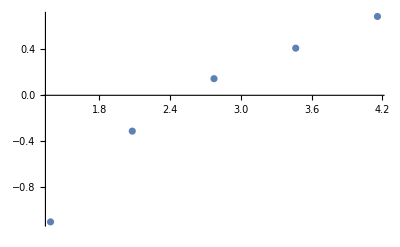

```mathematica
ListPlot[CvHeightPoints]
```

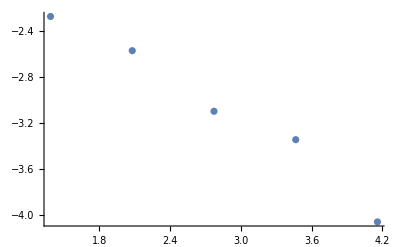

```mathematica
ListPlot[CvWidthPoints]
```

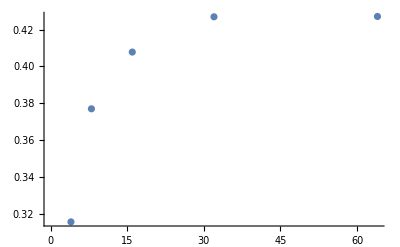

```mathematica
ListPlot[CvPosPoints]
```

```mathematica
CvHeightFit = NonlinearModelFit[CvHeightPoints,(sigmav) x + b, {{sigmav,0.5}, {b,0.5}},x,Weights->1/CvHeightErrors^2];
```

```mathematica
CvHeightFit[{"BestFit","ParameterTable"}]
```

{-2.27039+0.865476 x, | Estimate | Standard Error | t-Statistic | P-Value
sigmav | 0.865476 | 0.102769 | 8.42158 | 0.00351296
b | -2.27039 | 0.182468 | -12.4427 | 0.00111873}

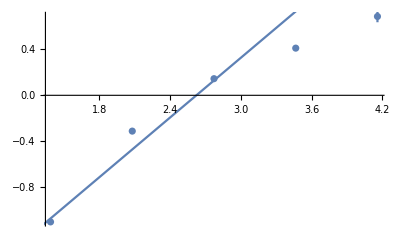

```mathematica
Show[
ErrorListPlot[Table[{CvHeightPoints[[i]][[1]],CvHeightPoints[[i]][[2]], CvHeightErrors[[i]]},{i,1,Length[CvHeightPoints]}]],
Plot[CvHeightFit[x],{x,0,5},PlotRange->Full]]
```

```mathematica
CvWidthFit = NonlinearModelFit[CvWidthPoints,-(1/v) x + b, {v, b},x,Weights->1/CvWidthErrors^2];
```

```mathematica
CvWidthFit[{"BestFit","ParameterTable"}]
```

{-1.59224-0.48903 x, | Estimate | Standard Error | t-Statistic | P-Value
v | 2.04486 | 0.185385 | 11.0304 | 0.00159587
b | -1.59224 | 0.070876 | -22.4651 | 0.000193133}

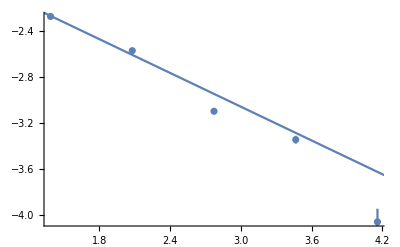

```mathematica
Show[
ErrorListPlot[Table[{CvWidthPoints[[i]][[1]],CvWidthPoints[[i]][[2]], CvWidthErrors[[i]]},{i,1,Length[CvWidthPoints]}]],
Plot[CvWidthFit[x],{x,0,5},PlotRange->Full]
]
```

```mathematica
CvPosFit = NonlinearModelFit[CvPosPoints, A*x^(-v) + b, {A,v, b},x,Weights->1/CvWidthErrors^2];
```

```mathematica
CvPosFit[{"BestFit","ParameterTable"}]
```

{0.442955-0.474848/x^0.948841, | Estimate | Standard Error | t-Statistic | P-Value
A | -0.474848 | 0.0145242 | -32.6935 | 0.000934259
v | 0.948841 | 0.0411844 | 23.0389 | 0.00187868
b | 0.442955 | 0.00357453 | 123.92 | 0.0000651145}

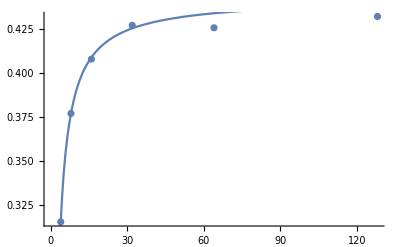

```mathematica
Show[
ErrorListPlot[Table[{CvPosPoints[[i]][[1]],CvPosPoints[[i]][[2]], CvPosErrors[[i]]},{i,1,Length[CvPosPoints]}]],
Plot[CvPosFit[x],{x,0.1,150},PlotRange->Full]
]
```

```mathematica
0.7429341769820177*1.8441672316663231
```

1.37009

```mathematica
SusceptHeight={{4,1.433738,0.0050138}, {8, 4.2354,0.015263},{16,13.2055966, 0.1015},{32, 42.582, 0.38578}, {64,141.934,2.34606},{128,472.449,8.02534}};
SusceptHeightPoints = Table[Log[{SusceptHeight[[i]][[1]],SusceptHeight[[i]][[2]]}], {i, 1, Length[SusceptHeight]}];
SusceptHeightErrors = Table[SusceptHeight[[i]][[3]]/SusceptHeight[[i]][[2]],{i,1,Length[SusceptHeight]}];
SusceptWidth={{4, 0.12460,0.000796 }, {8, 0.069091, 0.0006276}, {16,0.03763, 0.00047077}, {32, 0.01954, 0.0004501},{64, 0.00994924, 0.000361},{128,0.004800,0.000249}};
SusceptWidthPoints = Table[Log[{SusceptWidth[[i]][[1]],SusceptWidth[[i]][[2]]}], {i, 1, Length[SusceptWidth]}];
SusceptWidthErrors = Table[SusceptWidth[[i]][[3]]/SusceptWidth[[i]][[2]],{i,1,Length[SusceptWidth]}];
SusceptPos={{4, 0.17852967,0.0006346}, {8, 0.3156, 0.0003554}, {16,0.377971,0.000862583},{32,0.41023,0.000250 },{64,0.425546,0.000219},{128,0.433118,0.00012139 }};
SusceptPosPoints = Table[{SusceptPos[[i]][[1]],SusceptPos[[i]][[2]]}, {i, 1, Length[SusceptPos]}];
SusceptPosErrors = Table[SusceptPos[[i]][[3]],{i,1,Length[SusceptPos]}];
```

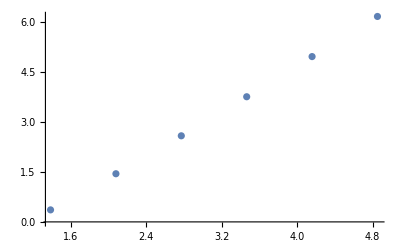

```mathematica
ListPlot[SusceptHeightPoints]
```

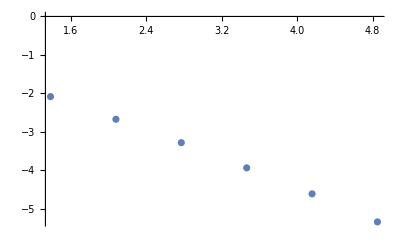

```mathematica
ListPlot[SusceptWidthPoints]
```

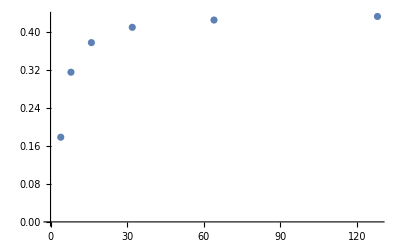

```mathematica
ListPlot[SusceptPosPoints]
```

```mathematica
SusceptHeightFit = NonlinearModelFit[SusceptHeightPoints,(sigmav) x + b, {{sigmav,0.5}, {b,0.5}},x,Weights->1/SusceptHeightErrors^2];
```

```mathematica
SusceptHeightFit[{"BestFit","ParameterTable"}]
```

{-1.9418+1.64223 x, | Estimate | Standard Error | t-Statistic | P-Value
sigmav | 1.64223 | 0.0217565 | 75.4824 | 1.84613×10^-7
b | -1.9418 | 0.0470362 | -41.2831 | 2.05762×10^-6}

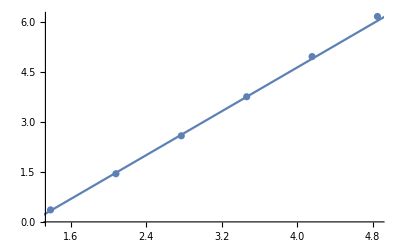

```mathematica
Show[
ErrorListPlot[
Table[{SusceptHeightPoints[[i]][[1]],SusceptHeightPoints[[i]][[2]], SusceptHeightErrors[[i]]},{i,1,Length[SusceptHeightPoints]}]],
Plot[SusceptHeightFit[x],{x,0,5},PlotRange->Full]
]
```

```mathematica
SusceptWidthFit = NonlinearModelFit[SusceptWidthPoints,-(1/v) x + b, {v, b},x,Weights->1/SusceptWidthErrors^2];
```

```mathematica
SusceptWidthFit[{"BestFit","ParameterTable"}]
```

{-0.835485-0.891867 x, | Estimate | Standard Error | t-Statistic | P-Value
v | 1.12124 | 0.0212336 | 52.8052 | 7.69851×10^-7
b | -0.835485 | 0.0345976 | -24.1486 | 0.0000174434}

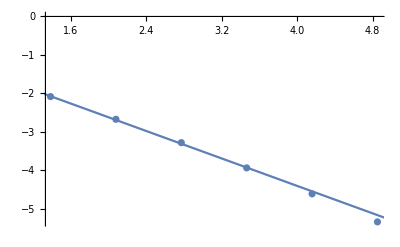

```mathematica
Show[
ErrorListPlot[Table[{SusceptWidthPoints[[i]][[1]],SusceptWidthPoints[[i]][[2]], SusceptWidthErrors[[i]]},{i,1,Length[SusceptWidthPoints]}]],
Plot[SusceptWidthFit[x],{x,0,5},PlotRange->Full]
]
```

```mathematica
SusceptPosFit = NonlinearModelFit[SusceptPosPoints, A*x^(-v) + b, {A,v, b},x,Weights->1/SusceptPosErrors^2];
```

```mathematica
CvPosFit[{"BestFit","ParameterTable"}]
```

{0.442955-0.474848/x^0.948841, | Estimate | Standard Error | t-Statistic | P-Value
A | -0.474848 | 0.0145242 | -32.6935 | 0.000934259
v | 0.948841 | 0.0411844 | 23.0389 | 0.00187868
b | 0.442955 | 0.00357453 | 123.92 | 0.0000651145}

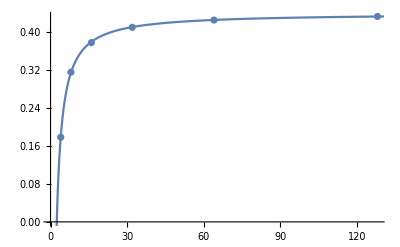

```mathematica
Show[
ErrorListPlot[Table[{SusceptPosPoints[[i]][[1]],SusceptPosPoints[[i]][[2]], SusceptPosErrors[[i]]},{i,1,Length[CvPosPoints]}]],
Plot[SusceptPosFit[x],{x,0.1,150},PlotRange->Full]
]
```

```mathematica
MagnetizationHeight = {{8, 0.90404375}, {16,0.841697265625}, {32,0.774832519531}, {64,0.711084960937}, {128, 0.659222839355}};
```

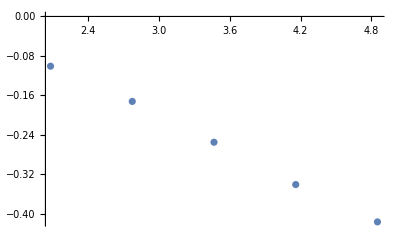

```mathematica
ListPlot[Log[MagnetizationHeight]]
```

```mathematica
MagnetizationHeightFit = NonlinearModelFit[Log[MagnetizationHeight],-(betav) x + b, {betav, b},x];
```

```mathematica
MagnetizationHeightFit[{"BestFit","ParameterTable"}]
```

{0.142935-0.115453 x, | Estimate | Standard Error | t-Statistic | P-Value
betav | 0.115453 | 0.00197076 | 58.5831 | 0.0000109572
b | 0.142935 | 0.00709809 | 20.1371 | 0.000267694}

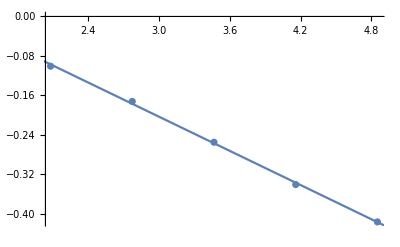

```mathematica
Show[ListPlot[Log[MagnetizationHeight]],Plot[MagnetizationHeightFit[x],{x,0,5}]]
```